```mathematica
(*Part 1*)
Clear["Global`*"]
g=9.81;
maxAngle=theta/.(Solve[2*V^2/g*Cos[2*theta]==0,theta][[2]]);
maxAngleDeg = maxAngle*180/Pi
vel=V/.(Solve[2*V^2/g*Sin[2*maxAngle]==1000, V][[2]])
vx = vel*Cos[maxAngle]
vy = vel*Sin[maxAngle]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

45.

70.0357

49.5227

49.5227

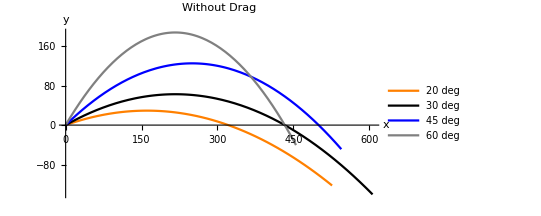

```mathematica
(*Part 2*)
Clear["Global`*"]
m=1;
g=9.81;
vel=70.03570517957252;

eqs = {x''[t]==0, y''[t]==-g};

(*20 deg*)
ini1= {x[0]==0, y[0]==0, x'[0]==vel * Cos[20.*Pi/180.], y'[0]==vel *  Sin[20.*Pi/180.]} ;
soln1=NDSolve[Join [eqs, ini1], {x,y}, {t, 0, 15}];

(*30 deg*)
ini2= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/6.], y'[0]==vel * Sin[Pi/6.]} ;
soln2=NDSolve[Join [eqs, ini2], {x,y}, {t, 0, 15}];

(*45 deg*)
ini3= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/4.], y'[0]==vel * Sin[Pi/4.]} ;
soln3=NDSolve[Join [eqs, ini3], {x,y}, {t, 0, 15}];

(*60 deg*)
ini4= {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/3.], y'[0]==vel * Sin[Pi/3.]} ;
soln4=NDSolve[Join [eqs, ini4], {x,y}, {t, 0, 15}];

p1=ParametricPlot[{x[t], y[t]}/.soln1, {t, 0,8},
	PlotLegends->{"20 deg"},
	PlotStyle->Orange];

p2=ParametricPlot[{x[t], y[t]}/.soln2, {t, 0,10},
	PlotLegends->{"30 deg"},
	PlotStyle->Black];

p3=ParametricPlot[{x[t], y[t]}/.soln3, {t, 0,11},
	PlotLegends->{"45 deg"},
	PlotStyle->Blue];

p4=ParametricPlot[{x[t], y[t]}/.soln4, {t, 0,13},
	PlotLegends->{"60 deg"},
	PlotStyle->Gray];

Show[{p1, p2, p3, p4}, AxesLabel->{x, y},PlotRange->All, PlotLabel->"Without Drag"]
```

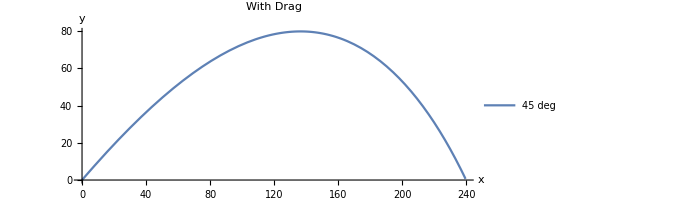

```mathematica
(*Part 3*)
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
vel=70.03570517957252;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};
ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[Pi/4.], y'[0]==vel * Sin[Pi/4.]};
soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 15}];

ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 8},
	AxesLabel->{x, y},
	PlotLabel->"With Drag",
	PlotLegends->{"45 deg"}]
```

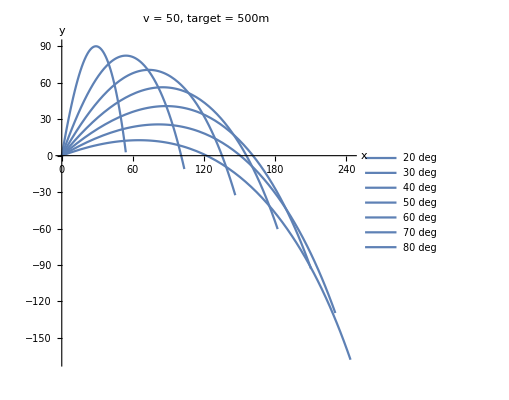

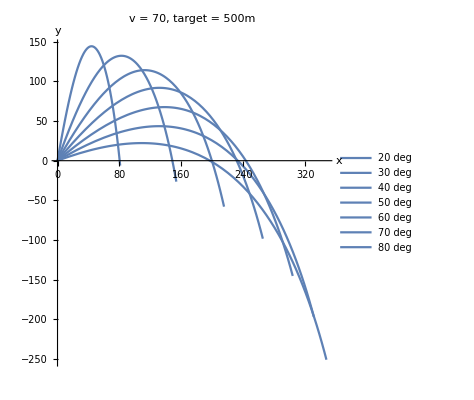

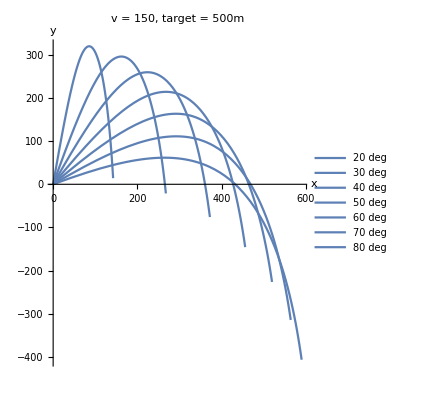

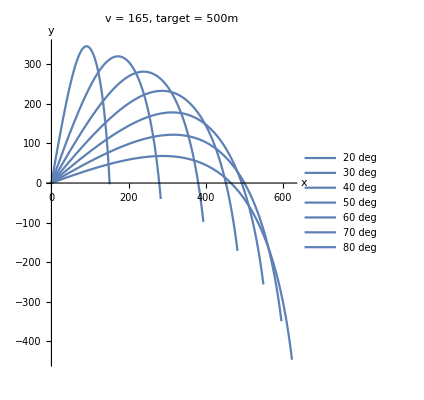

```mathematica
(*Part 4b*)
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
vel=50;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};

plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 1000}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 8.5},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 500m", vel]]

Clear[vel]
vel=70;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 11},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 500m", vel]]

Clear[vel]
vel=150;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 16},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 500m", vel]]

Clear[vel]
vel=165;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 17},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 500m", vel]]
(* Could not figure out how to put different colours for each angle *)

(* For v < 100 the optimal firing angle is ~40 deg *)
(* For v > 100 the optimal firing angle is ~30 deg *) 
(* As v increases the optimal firing angle decreases (see below) *)
```

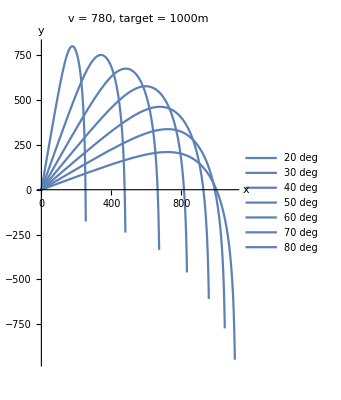

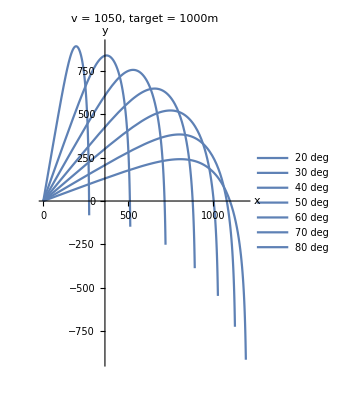

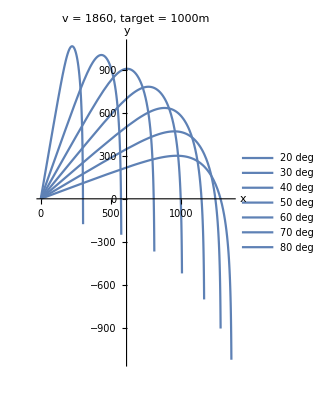

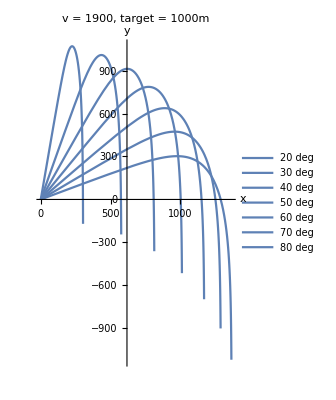

```mathematica
(*Part 4b*)
Clear["Global`*"]
v=Sqrt[x'[t]^2+y'[t]^2];
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
vel=780;
drag = rho*A*v^2;

eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};

plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 30},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 1000m", vel]]

Clear[vel]
vel=1050;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 30},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 1000m", vel]]

Clear[vel]
vel=1860;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 35},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 1000m", vel]]

Clear[vel]
vel=1900;
plots = Do[{
	theta = d * Pi / 180.,
	ini = {x[0]==0, y[0]==0, x'[0]==vel * Cos[theta], y'[0]==vel * Sin[theta]},
	soln=NDSolve[Join [eqs, ini], {x,y}, {t, 0, 50}],
	Sow[ParametricPlot[{x[t], y[t]}/.soln, {t, 0, 35},
	PlotLegends->{StringForm["`` deg", d]}]]
},{d, 20, 80, 10}]//Reap;
Show[plots[[2,1]], 
	AxesLabel->{x,y},
	PlotRange->All,
	PlotLabel->StringForm["v = ``, target = 1000m", vel]]
(*Could not figure out how to put different colours for each angle*)
```

```mathematica
(*Part 5*)
Clear["Global`*"]
m=0.5;
g=9.81;
rho=1.3;
A=0.05^2/2;
drag = rho*A*v^2;

(*Computes landing time given initial angle and velocity*)
landTime[theta0_, v1_]:= 
Module[{theta=theta0, v0=v1}, 
d = theta*Pi/180;
v=Sqrt[x'[t]^2+y'[t]^2];
eqs = {x''[t]==-(drag/m )* (x'[t]/v), y''[t]==-g-(drag/m)(y'[t]/v)};
ini = {x[0]==0, y[0]==0, x'[0]==v0* Cos[d],y'[0]==v0* Sin[d]};
soln = NDSolve[Join [eqs, ini], {x,y}, {t, 0, 100}];
time=FindRoot[y[t]/.soln[[1,2]],{t,100}];
vals = {time, x/.soln[[1,1]]};
Return[vals]
]

(*Computes range given initial angle and velocity*)
range[theta0_, v0_]:=
Module[{theta=theta0, v=v0},
vals = landTime[theta, v];
time = vals[[1,1,2]];
x0=vals[[2]];
distance = x0[time];
Return[distance]
];

(*Finds velocity required for a certain range given initial angle*)
(*Implements the binary search algorithm*)
findVel[theta0_, Range_]:=
Module[{theta=theta0,r=Range},
vStart = 0.;
vEnd=1000.;
vHalf = (vStart+vEnd)/2.;
xMax = range[theta, vHalf];
While [xMax≠r,
If[xMax>r,{
vEnd=vHalf;
vHalf = (vStart+vEnd)/2.;
xMax= range[theta, vHalf];
},{
vStart=vHalf;
vHalf = (vStart+vEnd)/2.;
xMax= range[theta, vHalf];
}];
];
Return[vHalf];
]

findVel[40, 500]

(*Finds the angle for a certain range with the minimum initial velocity*)
(*Implements the golden section search algorithm*)
findMinAngle[Range_]:=
Module[{r=Range},
start=1.;
end=70.;
a=end-(end-start)/(1.618);
aTest = start+(end-a);
thresh=1;
interval=Abs[end-start];
Print["thresh ",thresh];
Print["interval ",interval];

While[interval>thresh,{
startVel=findVel[start, r];
endVel =findVel[end, r];
aVel=findVel[a, r];
testVel=findVel[aTest,r];

If[Min[startVel, endVel, aVel, testVel]==aVel,{
end = aTest;
aTest= a;
a=end-(end-start)/(1.618)
},{
start=a;
a=aTest;
aTest=start+(end-a);
}];
interval=Abs[end-start];
Print["interval ",interval];
Print["proposed: ", (start+end)/2.];
}];
Return[(start+end)/2.]
]

findMinAngle[80]
```

168.821

thresh 1

interval 69.